#### This file used to be BC_LatticeOfClosestSigmaMaps.

#### Run Sections 1 and 2 of Cumulative, including the usual preliminaries. Probably use the NodePt command that gives the more symmetric lattice. Be sure to run any needed OutputFors, especially in connection with nm3.

## User choices (for plotting)

```mathematica
WantDetails="noWantDetails";
```

```mathematica
PrintFigures=False;
```

```mathematica
MatrixNote[Tmat]
mdir
odir=FileNameJoin[{mdir,"pdf_print"}]
otag=FileNameJoin[{odir,"BC_LatticeOfNodeMaps_"<>Tlab[Tmat]<>"_"}]
```

T is BrownAn00

/Users/carltape/mma

/Users/carltape/mma/pdf_print

/Users/carltape/mma/pdf_print/BC_LatticeOfNodeMaps_BrownAn00_

#### All are subject to change later :

```mathematica
(* options:={ViewPoint->eye,Lighting->{{"Ambient",White}},Boxed->False};
eye=50xyzTP[{30Degree,65Degree}];
imagesize=800;
ShiftToEye=.02;
tknsForGC=.008;  (* thickness of the green great circle on the XISO spheres *)
hueGreen=Hue[.4,1,.8]
 *)
```

```mathematica
PrintEye;
AngRadDisk
hueGreen
hueGray
hueBlue
```

eye = {39.24,22.66,21.13};  (θ, ϕ)_eye = {30,65}, ρ_eye = 50

0.0349066

Hue[0.4, 1, 0.8]

GrayLevel[0.6]

RGBColor[0.22566184, 0.35451528, 0.93616248]

#### legend options

```mathematica
hw=1.1;fontsize=15;increment=1;offset=2.6;
WantRound="NoWantRound";
(*WantRound="WantRound";*)
```

```mathematica
(* UforNM1=XRot[-20Degree]; *)
```

```mathematica
(* UforNM1=id; *)
```

```mathematica
ξXISO=0 Degree;  (* rotation angle about closest XISO axis; this is for U for nm1 *)
```

#### Functions

```mathematica
fact=1.05;
TextCenter[ISO]  :=NodePt[ISO]   -fact{.57,-.2};
TextCenter[XISO]:=NodePt[XISO]+fact{.62,0};
TextCenter[TRIG]:=NodePt[TRIG]+fact{.62,0};
TextCenter[CUBE]:=NodePt[CUBE]-fact{.61,0};
TextCenter[TET]  :=NodePt[TET ] -fact{.61,0};
TextCenter[ORTH]:=NodePt[ORTH]-fact{.61,0};
TextCenter[MONO]:=NodePt[MONO]-fact{.62,0};
TextCenter[TRIV]:=NodePt[TRIV]-fact{.63,0};
```

```mathematica
TextCenterMid[ ΣA_,ΣB_] :=NodePt[ΣA] +TextCenterT[ΣA,ΣB](NodePt[ΣB]-NodePt[ΣA]);
TextCenterT[TRIV,MONO] :=0.5;
TextCenterT[MONO,ORTH] :=0.5;
TextCenterT[ORTH,TET] :=0.5;
TextCenterT[TET,CUBE] :=0.5;
TextCenterT[CUBE,ISO] :=0.5;
TextCenterT[MONO,TRIG] :=0.5;
TextCenterT[TRIG,XISO] :=0.5;
TextCenterT[XISO,ISO] :=0.5;
TextCenterT[TRIG,CUBE] :=0.65;
TextCenterT[TET,XISO] :=0.65;
```

## Various tests

#### Experiment with your Tmat (color choices set in BC_ChooseTmat.nb)

```mathematica
(* npts =10000;
AlphaMONOvalues=Sort[Table[Alpha[Tmat,{RandomReal[{-π,π}],RandomReal[{0,π}]},MONO]/Degree,{k,npts}]];
Take[AlphaMONOvalues,5]
Take[AlphaMONOvalues,-5]*)
```

#### Optional test :

T is BrownAn00

{0,2,4,6,8,10,12,14,16,18,20,22,24}

22

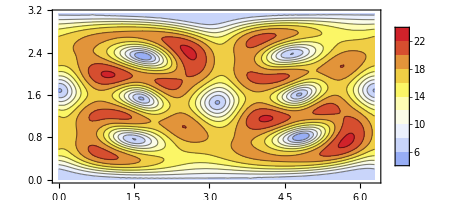

```mathematica
MatrixNote[Tmat]
contours[Tmat]
MaxForScaling[Tmat]
cpMONOprelim[Tmat,contours[Tmat],Automatic,MaxForScaling[Tmat]]
```

#### Adjust PaxesForLattice is you do not like the looks of the axes on the spheres.

```mathematica
PaxesForLattice=Paxes[True,True,True,id,{0,0,0},1.35,1,.17,.009,"Gray",ArrowColor];
```

#### Optional test :

```mathematica
MatrixNote[Tmat]
Print["contours = ",contours[Tmat]];
Print["MaxForScaling = ",MaxForScaling[Tmat]];
PrintEye;
Show[{cpMONO[Tmat,contours[Tmat],MaxForScaling[Tmat]],Graphics3D[PaxesForLattice]},options]
```

T is BrownAn00

contours = {0,2,4,6,8,10,12,14,16,18,20,22,24}

MaxForScaling = 22

eye = {39.24,22.66,21.13};  (θ, ϕ)_eye = {30,65}, ρ_eye = 50

-Graphics3D-

#### Optional test :

#### SmatOfΣ[Σ, Tmat, Σn, nm2] and SmatOfΣ[Σ, Tmat, Σn, nm3] should be the same for Σ = MONO

```mathematica
MatrixForm[SmatOfΣ[MONO,Tmat,Σn,nm2]-SmatOfΣ[MONO,Tmat,Σn,nm3]]
```

(0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0.)

#### Optional test with UTforTwoFoldGraphics

```mathematica
MatrixNote[Tmat]
nm=nm1;
Σ=ORTH;
(* UforNM1=Simplify[XRot[20Degree]]; *)
Print["U = ",MatrixForm[UforNM1]];
Print["Σ = ",Σ];
Print["contours = ",contours[Tmat]];
Print["MaxForScaling = ",MaxForScaling[Tmat]];
PrintEye;
(* Show[{cpMONO[SmatOfΣ[Σ,Tmat,dummy,nm],contours[Tmat],MaxForScaling[Tmat]],
Graphics3D[{PaxesForLattice,
TwoFoldGraphics[Σ,UforNM1,AngRadDisk,ShiftToEye,eye,tknsForGC,hueGreen]}]},Boxed->False,Lighting->{{"Ambient",White}},ViewPoint->eye] *)
```

T is BrownAn00

U = (0.921451 | -0.368714 | -0.12239
-0.365504 | -0.929543 | 0.0485472
-0.131666 | 0. | -0.991294)

Σ = ORTH

contours = {0,2,4,6,8,10,12,14,16,18,20,22,24}

MaxForScaling = 22

eye = {39.24,22.66,21.13};  (θ, ϕ)_eye = {30,65}, ρ_eye = 50

```mathematica
hueGreen
```

Hue[0.4, 1, 0.8]

```mathematica
PrintEye;
Row[{Graphics3D[{DummySphereGraphics[hueGray],PaxesForLattice},ViewPoint->eye,Boxed->False,Lighting->"Neutral",ImageSize->200],
      Graphics3D[{DummySphereGraphics[hueGreen],PaxesForLattice},ViewPoint->eye,Boxed->False,Lighting->"Neutral",ImageSize->200], 
     Graphics3D[{DummySphereGraphics[hueBlue],PaxesForLattice},ViewPoint->eye,Boxed->False,Lighting->"Neutral",ImageSize->200]}]
```

eye = {39.24,22.66,21.13};  (θ, ϕ)_eye = {30,65}, ρ_eye = 50

-Graphics3D--Graphics3D--Graphics3D-

```mathematica
ColorData["TemperatureMap"][.2]
```

RGBColor[0.5289344, 0.6284518, 0.9560588]

```mathematica
ListSigmaForColoredBalls[nm_,Σn_]:=If[nm===nm3,range[Σn],ListSigmaAll]; 
ListSigmaForGrayBalls[nm_,Σn_]:=ListComplement[ListSigmaAll,ListSigmaForColoredBalls[nm,Σn]];
```

```mathematica
(* Σn=ΣnXISO *)
ListSigmaForColoredBalls[nm3,Σn]
ListSigmaForColoredBalls[nm2,Σn]
ListSigmaForGrayBalls[nm2,Σn]
ListSigmaForGrayBalls[nm3,Σn]
```

{TRIV,MONO,ORTH,TET,XISO,ISO}

{TRIV,MONO,ORTH,TET,XISO,ISO,TRIG,CUBE}

{}

{TRIG,CUBE}

#### TESTING If the contours do not look clean, then add PlotPoints -> 30 or so in cpMONOprelim in common_funs.nb

```mathematica
(*Show[cpMONO[SmatOfΣ[XISO,Tmat,Σn,nm2],contours[Tmat],MaxForScaling[Tmat]],options]*)
```

#### Depends on what you are trying to do :

```mathematica
(* OutputFor[Tmat,TRIG] *)
```

```mathematica
(* OutputFor[Tmat,CUBE] *)
```

```mathematica
(* TextNM[nm1]=1;
TextNM[nm2]=2;
TextNM[nm3]=3; *)
```

## Main function for plotting the lattice of node maps

#### The setting increment = n prints every n^th contour label on the legend

```mathematica
LatticeFigText[Tmat_,Σn_,nm_]:=(Print[MatrixNote[Tmat]];  
Print[TextNodeMode[nm]];
If[nm===nm3,Print[range[Σn]]];
If[nm===nm1,Print["U = ",MatrixForm[UforNM1]]];
Print["contours = ",contours[Tmat],", MaxForScaling = ",MaxForScaling[Tmat]];
Print["AngRadDisk = ",AngRadDisk/Degree,", ShiftToEye = ",ShiftToEye];
PrintEye;)
```

#### I changed the lighting for the gray balls and XISO ball. Change back if you prefer.

```mathematica
solidlighting="Neutral";
solidlighting={{"Ambient",White}};
precisionUnm1=0.01;
```

```mathematica
Ginterball[Σ1_,Σ2_,Σn_,nm_]:=
If[Or[nm=!=nm3,MemberQ[range[Σn],Σ1]&&MemberQ[range[Σn],Σ2]],
Text[Framed[Style[Round[AngleMatrix[SmatOfΣ[Σ1,Tmat,Σn,nm],SmatOfΣ[Σ2,Tmat,Σn,nm]]/Degree,.1]^Style["∘",16imagesize/800],16 imagesize/800],Background->White,FrameMargins->Medium,FrameStyle->None],TextCenterMid[Σ1,Σ2]]];
```

```mathematica
x0=.85 NodePt[ORTH][[1]];
y0=.5 NodePt[TRIV][[2]];
```

```mathematica
LatticeFigure[Tmat_,Σn_,nm_]:=Graphics[{LatticeBlank,
Text[SequenceForm[SubscriptBox[Style[SymNM[nm],{Bold,17imagesize/800}],Style["TRIV",  11imagesize/800]]//DisplayForm,Style[SequenceForm["(",TextNM[nm],")"],15imagesize/800],Style[" = ",{17imagesize/800}],Style["T",{Bold,17imagesize/800}]],TextCenter[TRIV]+{0,.065}],
Text[SequenceForm[SubscriptBox[Style[SymNM[nm],{Bold,17imagesize/800}],Style[#,  11imagesize/800]]//DisplayForm,Style[SequenceForm["(",TextNM[nm],")"],15imagesize/800]],TextCenter[#]+{0,.065}]&/@Drop[ListSigmaAll,1],  (* Subscript[S, Σ] *)
(* β between balls *)
Ginterball[TRIV,MONO,Σn,nm],Ginterball[MONO,ORTH,Σn,nm],Ginterball[ORTH,TET,Σn,nm],Ginterball[TET,CUBE,Σn,nm],Ginterball[CUBE,ISO,Σn,nm],Ginterball[MONO,TRIG,Σn,nm],Ginterball[TRIG,XISO,Σn,nm],Ginterball[XISO,ISO,Σn,nm],Ginterball[TRIG,CUBE,Σn,nm],Ginterball[TET,XISO,Σn,nm],  
(* β *)
Text[Style[SequenceForm["β = ",Round[AngleMatrix[Tmat,SmatOfΣ[#,Tmat,Σn,nm]]/Degree,.1]^Style["∘",16imagesize/800]],16imagesize/800],TextCenter[#]+{0,-.065}]&/@ListSigmaForColoredBalls[nm,Σn],  
(* U for nm1 *)
If[nm===nm1,Text[SequenceForm[Style["U",{17,Italic}],Style[" = ",17],Style[DispMat[UforNM1,2],16]],{x0,y0+.5 NodePt[MONO][[2]]}]],
 (* OPTIONAL: ξ angle for rotating UXISO *)
If[nm===nm1,If[False,Text[Style[SequenceForm[Subscript["ξ","XISO"]," = ",ξXISO/Degree,"°"],16],{x0,y0+.3 NodePt[MONO][[2]]}]]],
(* nm text label *)
Text[Style[SequenceForm["node mode is ",TextNM[nm]],16],{x0,y0+.2 NodePt[MONO][[2]]}],
(* Tmat text label *)
Text[Framed[Style[MatrixNote[Tmat],16],Background->White,FrameStyle->Black,FrameMargins->Medium ],{x0,y0+0.1 NodePt[MONO][[2]]}],
(* balls for all but TRIV and ISO *)
Inset[Show[{cpMONO[SmatOfΣ[#,Tmat,Σn,nm],contours[Tmat],MaxForScaling[Tmat]],
Graphics3D[{PaxesForLattice,
TwoFoldGraphics[#,UTforTwoFoldGraphics[#,Tmat,Σn,nm],AngRadDisk,ShiftToEye,eye,tknsForGC,hueGreen]}]},{options}],NodePt[#],Center,{-.9,.9}]&/@ListComplement[ListSigmaForColoredBalls[nm,Σn],{TRIV,ISO}],
(* gray balls *)
Inset[Graphics3D[{DummySphereGraphics[hueGray],PaxesForLattice},ViewPoint->eye,Lighting->solidlighting,Boxed->False],NodePt[#],Center,{-.9,.9}]&/@ListSigmaForGrayBalls[nm,Σn],
(* ball for TRIV *)
If[True,Inset[Show[{cpMONO[Tmat,contours[Tmat],MaxForScaling[Tmat]],
Graphics3D[PaxesForLattice]},{options}],NodePt[TRIV], Center,{-.9,.9}]],
(* ball for ISO *)
If[True,Inset[Graphics3D[{DummySphereGraphics[hueBlue],PaxesForLattice},ViewPoint->eye,Lighting->solidlighting,Boxed->False],NodePt[ISO],Center,{-.9,.9}]],   
(* legends *)
If[True,Inset[legends[contours[Tmat],MaxForScaling[Tmat],SubscriptBox[Style["α",18],Style["MONO",10]]//DisplayForm,hw,fontsize,increment,offset],{.06ww,0}+.6NodePt[MONO]+.4NodePt[ISO],Center,.4]]
},AspectRatio->Automatic,ImageSize->imagesize]
```

#### Temporary

```mathematica
(* Σn
nm=nm3
AngleToNextFrom[#,Tmat,Σn,nm]/Degree&/@Drop[domain[Σn],-1]
If[PrintFigures,Export[otag<>ToString[nm]<>".pdf",LatticeFigure[Tmat,Σn,nm]],LatticeFigure[Tmat,Σn,nm]] *)
```

## Gallery of figures

1-1-2024 5:54

T is BrownAn00

Node mode nm2: Closest to Tmat

contours = {0,2,4,6,8,10,12,14,16,18,20,22,24}, MaxForScaling = 22

AngRadDisk = 2., ShiftToEye = 0.02

eye = {39.24,22.66,21.13};  (θ, ϕ)_eye = {30,65}, ρ_eye = 50

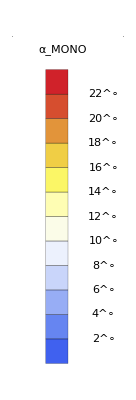
-Graphics-
-Graphics-

```mathematica
Print[DateSequence[DateList[],"yes"]];
nm=nm2;
LatticeFigText[Tmat,Σn,nm]
If[PrintFigures,Export[otag<>ToString[nm]<>".pdf",LatticeFigure[Tmat,Σn,nm]],LatticeFigure[Tmat,Σn,nm]]
```

#### nm1 with U set to the closest XISO (there is a text label for ξ that needs to be set to True)

```mathematica
nm=nm1;
UforNM1=UT[Tmat,XISO]; 
LatticeFigText[Tmat,Σn,nm]
If[PrintFigures,Export[otag<>ToString[nm]<>"_XISO.pdf",LatticeFigure[Tmat,Σn,nm]],LatticeFigure[Tmat,Σn,nm]]
```

T is BrownAn00

Node mode nm1: P(T,𝒱_Σ(U))

U = (0.921451 | -0.368714 | -0.12239
-0.365504 | -0.929543 | 0.0485472
-0.131666 | 0. | -0.991294)

contours = {0,2,4,6,8,10,12,14,16,18,20,22,24}, MaxForScaling = 22

AngRadDisk = 2., ShiftToEye = 0.02

eye = {39.24,22.66,21.13};  (θ, ϕ)_eye = {30,65}, ρ_eye = 50

$Aborted

#### nm1 with U set to the Identity

```mathematica
Print[DateSequence[DateList[],"yes"]];
nm=nm1;UforNM1=id;
LatticeFigText[Tmat,Σn,nm]
If[PrintFigures,Export[otag<>ToString[nm]<>"_Id.pdf",LatticeFigure[Tmat,Σn,nm]],LatticeFigure[Tmat,Σn,nm]]
```

#### Compare three node sequences (need to have run these in Cumulative). The list of angles is a check with the ones pre-computed in Cumulative.

```mathematica
nm=nm3;
If[PrintFigures,Export[otag<>ToString[nm]<>"_"<>StringDrop[ToString[ΣnTETXISO],2]<>".pdf",LatticeFigure[Tmat,ΣnTETXISO,nm]],LatticeFigure[Tmat,ΣnTETXISO,nm]]
AngleToNextFrom[#,Tmat,ΣnTETXISO,nm]/Degree&/@Drop[domain[ΣnTETXISO],-1]
If[PrintFigures,Export[otag<>ToString[nm]<>"_"<>StringDrop[ToString[ΣnTETCUBE],2]<>".pdf",LatticeFigure[Tmat,ΣnTETCUBE,nm]],LatticeFigure[Tmat,ΣnTETCUBE,nm]]
AngleToNextFrom[#,Tmat,ΣnTETCUBE,nm]/Degree&/@Drop[domain[ΣnTETCUBE],-1]
If[PrintFigures,Export[otag<>ToString[nm]<>"_"<>StringDrop[ToString[ΣnTRIGXISO],2]<>".pdf",LatticeFigure[Tmat,ΣnTRIGXISO,nm]],LatticeFigure[Tmat,ΣnTRIGXISO,nm]]
AngleToNextFrom[#,Tmat,ΣnTRIGXISO,nm]/Degree&/@Drop[domain[ΣnTRIGXISO],-1]
If[PrintFigures,Export[otag<>ToString[nm]<>"_"<>StringDrop[ToString[ΣnTRIGCUBE],2]<>".pdf",LatticeFigure[Tmat,ΣnTRIGCUBE,nm]],LatticeFigure[Tmat,ΣnTRIGCUBE,nm]]
AngleToNextFrom[#,Tmat,ΣnTRIGCUBE,nm]/Degree&/@Drop[domain[ΣnTRIGCUBE],-1]
```

## Optional: choose closest XISO for nm1, then rotate it by ξ about its symmetry axis

```mathematica
(* WantDetails="WantDetails";
OutputFor[Tmat,XISO]
MatrixForm[UT[Tmat,XISO]] *)
```

```mathematica
Clear[U]
```

```mathematica
UXISO=UT[Tmat,XISO];
MatrixForm[UXISO]
vXISO=UXISO.{0,0,1};
MatrixForm[vXISO]
RotXISO[U_,ξ_]:=ROT[ξ,U.{0,0,1}];
Urot[U_,ξ_]:=RotXISO[U,ξ].U;
```

#### The next two calculations are the same, because U Z_t = (U Z_t U^T)U and U Z_t U^T is rotation through angle t about U(0,0,1). See Theorem 2 of the submitted paper. You do not change 𝒱_XISO(U) if you replace U by UG, where G is in 𝔾_XISO. That is, G can be any rotation about the z-axis or any 2-fold rotation about a horizontal axis.

```mathematica
ξXISO=30Degree;
MatrixForm[Urot[UXISO,ξXISO]]
MatrixForm[UXISO.ZRot[ξXISO]]
```

```mathematica
(* Angle[UT[Tmat,XISO].{1,0,0},UT[Tmat,XISO].ZRot[30Degree].{1,0,0}]/Degree *)
```

```mathematica
nm=nm1;
UforNM1=id;
LatticeFigText[Tmat,Σn,nm]
(*LatticeFigure[Tmat,Σn,nm]*)
```

```mathematica
UforNM1=UXISO;
LatticeFigText[Tmat,Σn,nm]
(*LatticeFigure[Tmat,Σn,nm]*)
```

#### print a set of figures to files (by default, this is set to False, so no printing) directories are set in BC_ChooseTmat.nb

```mathematica
otag
otagg=otag<>ToString[nm]<>"_XISO_"
```

```mathematica
ξmin=0;
ξmax=120Degree;
dξ=15Degree;
If[False,Do[UforNM1=UXISO.ZRot[ξXISO];fig=LatticeFigure[Tmat,Σn,nm];
Export[otagg<>StringPadLeft[ToString[Round[ξXISO/Degree]],3,"0"]<>".pdf",fig ],{ξXISO,ξmin,ξmax,dξ}]]
```